```mathematica
(* 
A.Odrzywolek, NSE abundance data, Atomic Data and Nuclear Data Tables 98 (2012) 852-861
*)
```

```mathematica
Date[]
```

{2017,4,27,14,37,8.77329}

```mathematica
(* 800 isotopes NSE calculation, MAX 3181 from Wolfram database, 64-bit OS required(!?) for all nuclides *)
```

```mathematica
SetDirectory["/home/misiek/tmp/datasets/test8"]
```

/home/misiek/tmp/datasets/test8

```mathematica
(* SetDirectory["H://misiek//nse//datasetADNDTfigs/"] *)
```

```mathematica
(* 
SetDirectory["/mnt/E/temp/NSE_pn_table_tmp/"]
*)
```

```mathematica
myPrecision=96
```

96

```mathematica
MinPrecision=Max[50,myPrecision]
```

96

```mathematica
(* range of temperatures [MeV] and densities [kg/m^3] with grid size *)
```

```mathematica
(*T9tbl=Rationalize[{0.1,0.15,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.0,1.5,2.0,2.5,3.0,3.5,4.0,4.5,5.0,6.0,7.0,8.0,9.0,10.0},0.001] *)(* T9 from Hix&Thielemann nse.f*)
```

```mathematica
(* kTtoT9=116045/10000 *)
```

```mathematica
(* kTtbl=T9tbl/kTtoT9 *)
```

```mathematica
(* tempMAX=kTtbl[[-1]] *)
```

```mathematica
(* tempMIN=kTtbl[[1]] *)
```

```mathematica
(* Table[kTtbl[[ii]]-kTtbl[[ii-1]]//N,{ii,2,tempNum}]*)
```

```mathematica
tempMAX=1.0 //Rationalize
```

1

```mathematica
tempMIN=0.3 //Rationalize
```

3/10

```mathematica
Δtemp=0.05 //Rationalize
(* NOTE that temperature step must be small enough to provide accurate guess for the next step. Procedure starts with analytical approximation for p, n, He4 mixture for highest temperature, and slowly decrease kT. This procedure fails for kT<0.3 if step is too large.
In fact, it is combination of temperature and density, and for highest densities failure is more likely *)
```

1/20

```mathematica
(* tempNum=Dimensions[T9tbl][[1]]*)
```

```mathematica
(* tempNum=Table[,{temp,tempMIN,tempMAX,Δtemp}] //Dimensions //First*)
```

```mathematica
kTtbl=Table[kT,{kT,tempMIN,tempMAX,Δtemp}] ;
```

```mathematica
tempNum=Dimensions[kTtbl][[1]]
```

15

```mathematica
Export["data/kT.dat",ToString[kTtbl//N]<>"\n\n","Text"]
```

data/kT.dat

```mathematica
lgdensMAX=10
```

10

```mathematica
lgdensMIN=6
```

6

```mathematica
Δlgdens=0.5 //Rationalize
```

1/2

```mathematica
lgdenstbl=Table[lgdens,{lgdens,lgdensMIN, lgdensMAX, Δlgdens}]
```

{6,13/2,7,15/2,8,17/2,9,19/2,10}

```mathematica
lgdensNum=lgdenstbl//Dimensions//First
```

9

```mathematica
Export["data/lg_rho.dat",ToString[lgdenstbl//N]<>"\n\n","Text"]
```

data/lg_rho.dat

```mathematica
(* NOTE: it is better to use rational steps for Ye, because numerical
values might look identical, while they are not, e.g.: 0.35, 0.35000000
In worst case you will get repeated or extremely close entries !
*)
```

```mathematica
YeFINE=Table[Ye,{Ye,0.35,0.55,0.025}]//Rationalize (* more dense tabulation in rapid variation region *)
```

{7/20,3/8,2/5,17/40,9/20,19/40,1/2,21/40,11/20}

```mathematica
Ye1=Table[Ye,{Ye,0.05,0.35,0.05}]//Rationalize (* TODO: Ye very small 0.01, 0.001 etc.*; maybe scalling density from Ye=0.1 ? Results does not seem to change...
*)
```

{1/20,1/10,3/20,1/5,1/4,3/10,7/20}

```mathematica
Ye2=Table[Ye,{Ye,0.55,0.95,0.05}]//Rationalize
```

{11/20,3/5,13/20,7/10,3/4,4/5,17/20,9/10,19/20}

```mathematica
(* YeMAX = Count[Table[Import["E:/temp/np_800_"<>ToString[NumberForm[N[Ye],{4,4}]]<>".dat"],{Ye,ΔYe,0.5,ΔYe}],$Failed]/1000 *)
```

```mathematica
Yetbl=Union[{0,1/1000,1/100},Ye1, YeFINE,Ye2,{99/100,999/1000,1}]//Sort (* Sort is not required, Union should do this *)
```

{0,1/1000,1/100,1/20,1/10,3/20,1/5,1/4,3/10,7/20,3/8,2/5,17/40,9/20,19/40,1/2,21/40,11/20,3/5,13/20,7/10,3/4,4/5,17/20,9/10,19/20,99/100,999/1000,1}

```mathematica
YeNum=Yetbl//Dimensions//First
```

29

```mathematica
ToString[Yetbl//N]
```

{0., 0.001, 0.01, 0.05, 0.1, 0.15, 0.2, 0.25, 0.3, 0.35, 0.375, 0.4, 0.425, 0.45, 0.475, 0.5, 0.525, 0.55, 0.6, 0.65, 0.7, 0.75, 0.8, 0.85, 0.9, 0.95, 0.99, 0.999, 1.}

```mathematica
Export["data/Ye.dat",ToString[Yetbl//N]<>"\n\n","Text"]
```

data/Ye.dat

```mathematica
(* iso800=Take[Delete[IsotopeData[],{{9},{18}}],{1,800}] ; *)
(* 
Mechanical use of large databases requires caution. Deleted positions are Helium2 and Lithium3, included in the databases for historical reasons. Lithium3 drastically changes results for large Ye, because it replaces protons! 

For beginners, I recommend use hand-crafted selections below from well-established published sources 
*)
```

```mathematica
isoP={"Neutron","H1","He4","C12","O16","Ti44","Fe54","Fe56","Ni56","Ni62","Co57"};
(* Minimal astrophysically-motivated selection of nuclides *)
```

```mathematica
iso32={"Neutron","Hydrogen1","He4","C12","O16","Ne20","Mg24","Si28","S32","Ar36","Ca40","Ti44","Ti50","Cr48","Cr54","Cr55","Mn54","Mn55","Mn56","Fe52","Fe54","Fe55","Fe56","Fe57","Fe58","Co55","Co56","Ni56","Ni57","Ni58","Ni60","Zn60"};
(* MPA-Garching HOTB iso32 network *)
```

```mathematica
isoFXT={"Neutron","Hydrogen1","He4","C12","C13","N13","N14","O14","O15","O16","O17","O18","F17","F18","F19","Ne18","Ne19","Ne20","Mg22","Mg24","Al27","Si28","P31","S30","S32","Cl35","Ar36","K39","Ca40","Ti44","Cr48","Cr49","Cr50","Cr51","Cr52","Cr53","Cr54","Fe52","Fe54","Fe55","Fe56","Fe57","Fe58","Co55","Ni56","Ni58"};
(* F.X.Timmes NSE calculations from cococubbed.com *)
```

```mathematica
isoSimplest={"Neutron","Hydrogen1","Helium4"};
(* Simplest possible case. Useful for debugging, analytical estimates, and for high temperatures *)
```

```mathematica
(* NOTE: isotope set must include Neutron and Hydrogen1 *)
```

```mathematica
IsotopeData[Entity["Isotope","Helium4"],"Spin"]
```

0

```mathematica
iso=(IsotopeData[#]&)/@isoSimplest
```

{Entity[Isotope,Neutron],hydrogen,helium-4}

```mathematica
iso[[-1]]//FullForm
```

Entity["Isotope","Helium4"]

```mathematica
CommonName@%
```

helium-4

```mathematica
CanonicalName@%%
```

Helium4

```mathematica
FullForm@%
```

"Helium4"

```mathematica
?Entity
```

Entity[type,name] represents an entity of specified type identified by name.

```mathematica
Export["data/isotopes.dat",CanonicalName/@iso]
```

data/isotopes.dat

```mathematica
niso=Dimensions[iso][[1]]
```

3

```mathematica
(* 
BUG?: ponizej potencjalny blad: nie jest oczywiste, ze ostatnie jadro atomowe na liscie ma najwiecej neutronow i protonow! Nalezy przeszukac cala liste 
*)
```

```mathematica
IsotopeData[#,"AtomicNumber"]&/@iso
```

{0,1,2}

```mathematica
IsotopeData[#,"NeutronNumber"]&/@iso//Max
```

2

```mathematica
(* Zmax=IsotopeData[iso[[-1]],"AtomicNumber"] +3 Max. atomic number *)
(* Nmax=IsotopeData[iso[[-1]],"NeutronNumber"] +2 Max. neutron number *)
```

```mathematica
Zmax=(IsotopeData[#,"AtomicNumber"]&/@iso//Max )(* Max. atomic number *)
Nmax=(IsotopeData[#,"NeutronNumber"]&/@iso//Max)(* Max. neutron number *)
```

2

2

```mathematica
nseH="#define kT_MIN_nse "<>ToString[tempMIN //N] <>"\n"<>
"#define kT_MAX_nse "<>ToString[tempMAX //N] <>"\n"<>
"#define N_kT_nse " <> ToString[tempNum]<>"\n"<>
"#define lg_rho_MIN_nse "<>ToString[lgdensMIN //N] <>"\n"<>
"#define lg_rho_MAX_nse "<>ToString[lgdensMAX //N] <>"\n"<>
"#define N_lg_rho_nse " <> ToString[lgdensNum]<>"\n" <>
"#define N_Ye_nse "<>ToString[YeNum] <>"\n"<>
"#define niso "<>ToString[niso]<>"\n"<>
"#define Z_max_nse "<>ToString[Zmax+1]<>"\n"<>
"#define N_max_nse "<>ToString[Nmax+1]<>"\n";
```

```mathematica
Export["data/nse_tbl.h",nseH,"Text"]
```

data/nse_tbl.h

```mathematica
(* NOTE: It is assumed below that nuclei list is sorted! Last in the list is used to determine max. Z and A *)
```

```mathematica
nuclideTBL=Table[If[Position[iso,IsotopeData[{ii,ii+jj},"StandardName"]]=={},-1,Position[iso,IsotopeData[{ii,ii+jj},"StandardName"]][[1,1]]-1],{ii,1,Zmax},{jj,1,Nmax}];
```

```mathematica
Prepend[Table[-1,{ii,1,Nmax-1}],0] ;
```

```mathematica
Prepend[nuclideTBL,%] ;
```

```mathematica
Transpose[%];
```

```mathematica
Table[If[ii==1,1,-1],{ii,0,Zmax}];
```

```mathematica
Prepend[%%,%];
```

```mathematica
nuclideTBLfinal=Transpose[%];
```

```mathematica
magick={{2,1},{9,8},{17,16},{21,20},{29,28},{51,50},{Nmax+1,Nmax}};
```

```mathematica
MatrixPlot[nuclideTBLfinal, DataReversed->{True,False},Mesh->True, FrameTicks->{ magick,magick,None ,None },ColorRules->{-1->White,_->Black},FrameLabel->{"Z","N"}]
```

-Graphics-

```mathematica
Export["data/Nuclide_chart.pdf",%]
```

data/Nuclide_chart.pdf

```mathematica
Dimensions[nuclideTBLfinal]
```

{3,3}

```mathematica
Export["data/N_Z_tbl.dat",ToString[nuclideTBLfinal]<>"\n","Text"]
```

data/N_Z_tbl.dat

```mathematica
id=Table[{QuantityMagnitude[IsotopeData[iso[[ii]],"BindingEnergy"],"MeV"],IsotopeData[iso[[ii]],"Symbol"],IsotopeData[iso⟦ii⟧,"AtomicNumber"],IsotopeData[iso[[ii]],"NeutronNumber"],IsotopeData[iso[[ii]],"MassNumber"],IsotopeData[iso[[ii]],"Spin"],ii},{ii,1,niso,1}]
```

{{0.,^1n,0,1,1,1/2,1},{0.,^1H,1,0,1,1/2,2},{7.073915,^4He,2,2,4,0,3}}

```mathematica
tbl=SetPrecision[id /._Missing->0,myPrecision]//Rationalize;
```

```mathematica
(* SetPrecision[id,100] ;*)
```

```mathematica
X=Table[,{i,1,niso}];
```

```mathematica
(* Temperature dependend partition function *)
```

```mathematica
iso[[-1]]
```

helium-4

```mathematica
iso⟦-1⟧
```

helium-4

```mathematica
QuantityMagnitude[IsotopeData[iso[[-1]],"ExcitedStateEnergies"],"MeV"]
```

{20.21,21.01,21.84,23.33,23.64,24.25,25.28,25.95,27.42,28.31,28.37,28.39,28.64,28.67,29.89}

```mathematica
FullForm[%[[1]]]
```

1.4082

```mathematica
e=Table[SetPrecision[QuantityMagnitude[IsotopeData[iso[[ii]],"ExcitedStateEnergies"],"MeV"],myPrecision] ,{ii,1,niso}]
```

{QuantityMagnitude[{},MeV],QuantityMagnitude[{},MeV],QuantityMagnitude[$Failed,MeV]}

```mathematica
QuantityMagnitude[e[[11,1]],"MeV"]
```

Quantity::compat: DimensionlessUnit and Megaelectronvolts are incompatible units

QuantityMagnitude[1.2239800000000000000026194324487249787125620059669017791748046875,MeV]

```mathematica
jEXP=Table[IsotopeData[iso[[ii]],"ExcitedStateSpins"] ,{ii,1,niso}] ;
```

```mathematica
j=Table[Table[
Switch[
Dimensions[jEXP[[ii,i]]],
{},jEXP[[ii,i]],(* Spin known *)
{1},0,(* Spin unknown *)
{2},jEXP[[ii,i]][[2,1]]],(* Spin uncertain: first taken [avg. or random possible, but difficult to reproduce!] *)
{i,1,Dimensions[jEXP[[ii]]][[1]]}],{ii,1,niso}];
```

```mathematica
(* TODO: third-party partition function!*)
```

```mathematica
kTtbl
```

{3/10,7/20,2/5,9/20,1/2,11/20,3/5,13/20,7/10,3/4,4/5,17/20,9/10,19/20,1}

```mathematica
GkT= Table[Sum[(2*j[[ii,i]]+1)*Exp[-e[[ii,i]]/kT],{i,1,Dimensions[e[[ii]]][[1]]}],{ii,1,niso}];
```

```mathematica
LaunchKernels[4](* calculate partition function in parallel *)
```

{KernelObject[1,local],KernelObject[2,local],KernelObject[3,local],KernelObject[4,local]}

```mathematica
DistributeDefinitions[GkT,tempMIN,tempMAX,kTtbl]
```

{GkT,tempMIN,tempMAX,kTtbl}

```mathematica
GkTtbl=ParallelTable[Table[If[kT==0,0,GkT[[ii]]],{kT,kTtbl}],{ii,1,niso}];
```

```mathematica
Export["data/GkTtbl.m",GkTtbl]
```

data/GkTtbl.m

```mathematica
GkTtbl=Import["data/GkTtbl.m"];
```

```mathematica
(* GkTtbl=SetPrecision[Import["data/GkT_002.dat","Table"],100];*)
```

```mathematica
(* Export["E://temp/GkT_002.dat",GkTtbl,"Table"] *)
```

```mathematica
GkTtbl//Dimensions
```

{11,15}

```mathematica
GkTtbl[[11,2]]
```

0.66970936823038664715145956489897511260706521527178169696158320276809139128706395557801147150652

```mathematica
GkTstring=StringJoin[Table[ToString[Chop[GkTtbl[[ii]] //N,10^-5] //N]<>",\n",{ii,1,niso-1}] ]<>ToString[Chop[GkTtbl[[-1]] //N,10^-5] //N] ;
```

```mathematica
(* ToExpression["{"<>GkTstring<>"}"]; Read this ^^^ using this line *)
```

```mathematica
GkTinterp=Table[Interpolation[Transpose[{kTtbl,GkTtbl[[ii]]}] ,InterpolationOrder->1],{ii,1,niso}];
```

```mathematica
G0=Table[2 tbl[[i,6]]+SetPrecision[1,myPrecision],{i,1,niso}] ;
```

```mathematica
G=Table[G0[[ii]]+GkTinterp[[ii]][kT],{ii,1,niso}];
```

```mathematica
(*
G=Table[G0[[ii]],{ii,1,niso}];
 Ground state partition function
*)
```

```mathematica
kTtblPrint=Table[kTtbl[[ii]],{ii,1,Dimensions[kTtbl][[1]],1}]//N
```

{0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.}

```mathematica
(* kTtblPrint={0.6,0.8,1.0,2.0,5.0,10.0}*)
```

```mathematica
kTtblPrintNum=Dimensions[kTtblPrint][[1]]
```

15

```mathematica
trunc=If[#<0.01,"0.00",ToString[PaddedForm[N[#],{3,2}]]]&
```

If[#1<0.01,0.00,ToString[N[Slot[ 1.00]]]]&

```mathematica
trunc[10^-3]
```

0.00

```mathematica
N[GkTinterp[[3]][0.6],4]
```

3.84754×10^-15

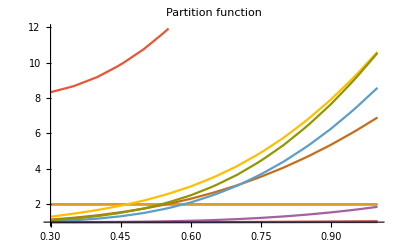

```mathematica
Plot[Evaluate[Table[G[[ii]],{ii,1,niso}]],{kT,tempMIN,tempMAX},PlotLabel->"Partition function"]
```

```mathematica
A=Table[tbl[[i,5]],{i,1,niso}]
```

{1,1,4,12,16,44,54,56,56,62,57}

```mathematica
Z=Table[tbl[[i,3]],{i,1,niso}]
```

{0,1,2,6,8,22,26,26,28,28,27}

```mathematica
Ne=Table[tbl[[i,4]],{i,1,niso}];
```

```mathematica
Q=Table[tbl[[i,1]]*tbl[[i,5]],{i,1,niso}] //Chop;
```

```mathematica
Export["data/A.dat",ToString[N[A]]<>"\n\n","Text"]
Export["data/Z.dat",ToString[N[Z]]<>"\n\n","Text"]
Export["data/N.dat",ToString[N[Ne]]<>"\n\n","Text"]
Export["data/Q.dat",ToString[N[Q]]<>"\n\n","Text"]
Export["data/G0.dat",ToString[N[G0]]<>"\n\n","Text"]
```

data/A.dat

data/Z.dat

data/N.dat

data/Q.dat

data/G0.dat

```mathematica
Export["data/GkT.dat",GkTstring<>"\n\n","Text"]
```

data/GkT.dat

```mathematica
qe=SetPrecision[1.6021892*10^(-19),myPrecision];
h=SetPrecision[6.626176 10^(-34),myPrecision];
k=SetPrecision[1.380662 10^(-23),myPrecision];
mp=SetPrecision[1.672  10^(-27),myPrecision];
```

```mathematica
T=kT 10^6 qe /k
```

1.1604499870352047187941951640223252011002445734839926390095863420747882972206812556863658766469×10^10 kT

```mathematica
Precision[T]
```

95.699

```mathematica
(* thermal de Broglie wavelength *)
```

```mathematica
λ=Sqrt[h^2/(2 Pi mp k T)]
```

1.6150947165848605696398405619854210875480289672409667454037866167531010455909107394516490255626×10^-14 √(1/kT)

```mathematica
(* abundance table *)
```

```mathematica
X = Table[(1/2)*G[[k]]*
     (1000ρ/(2*mp))^(A[[k]] - 1)*
     λ^(3*(A[[k]] - 1))*
     A[[k]]^(5/2)*Xn^Ne[[k]]*
     Xp^Z[[k]]*E^(Q[[k]]/kT), 
    {k, 1, niso}];
```

```mathematica
X[[1]]
```

1/2 Xn (2.+                        3
InterpolatingFunction[{{--, 1}}, <>]
                        10[kT])

```mathematica
(* sum of the abundances equals to 1 *)
```

```mathematica
eq1=Sum[X[[ii]],{ii,1,niso}]-1;
```

```mathematica
(* electron fraction *)
```

```mathematica
eq2=Sum[ Z[[ii]]/A[[ii]]* X[[ii]],{ii,1,niso}]-Ye;
```

```mathematica
eq11 = eq1 /. {Xn->10^n,Xp->10^p}  ;
eq22 = eq2 /. {Xn->10^n,Xp->10^p}  ;
```

```mathematica
(* ContourPlot[{eq11,eq22} /. kT->0.6,{n,-16,0},{p,-16,0},PlotPoints->15] *)
```

```mathematica
np=Table[{temp,lgdens,{,}},{temp,kTtbl},{lgdens,lgdenstbl}] ;
```

```mathematica
Dimensions[np]
```

{15,9,3}

```mathematica
J11=D[eq11,n]//Simplify;
```

```mathematica
J12=D[eq11,p]//Simplify;
```

```mathematica
J21=D[eq22,n]//Simplify;
```

```mathematica
J22=D[eq22,p]//Simplify;
```

```mathematica
(* TODO, ParallelTable - not easy in this form, some work required, np could be overwritten !  Each kernel must create own copy. Testing required !*)
```

```mathematica
Table[
For[kk=1, kk≤Dimensions[np][[2]],kk++,
For[ii=Dimensions[np][[1]];guessn=Log10[1-Ye];guessp=Log10[Ye],ii≥1,ii--,
temp = np[[ii,kk]][[1]];
dens = np[[ii,kk]][[2]];
sol=FindRoot[{eq11,eq22} /. {kT->temp,ρ->10^dens},{{n,guessn},{p,guessp}},WorkingPrecision->64, Jacobian->({{J11,J12},{J21,J22}}/. {kT->temp,ρ->10^dens}),MaxIterations->2000]; 
nse={Xn->10^n,Xp->10^p} /.sol;
guessn=n /.sol;
guessp=p /. sol;
np[[ii,kk,3]]={guessn,guessp};
abundances=X /. nse /. {kT->temp,ρ->10^dens};
If[Abs[Tr[abundances]-1]>10^-52,
Print["Ye=",Ye,"\tkT=",N[temp,3],"\t","lg ρ=",N[dens,3 ],"\t",Tr[abundances]-1,"\t",Select[Flatten[abundances],#>1&],"\t",Select[Flatten[abundances],#<0&]
](*If ends*)
]
];
 ];
   Export["data/np_P_GkT_"<>ToString[NumberForm[N[Ye],{4,4}]]<>".dat",Flatten[Table[{np[[ii,kk]][[1]],np[[ii,kk]][[2]],np[[ii,kk]][[3,1]],np[[ii,kk]][[3,2]]},{ii,1,Dimensions[np][[1]]},{kk,1,Dimensions[np][[2]]}],1],"Table"] 
,{Ye,Yetbl[[2;;-2]]}]
```

{data/np_P_GkT_0.0010.dat,data/np_P_GkT_0.0100.dat,data/np_P_GkT_0.0500.dat,data/np_P_GkT_0.1000.dat,data/np_P_GkT_0.1500.dat,data/np_P_GkT_0.2000.dat,data/np_P_GkT_0.2500.dat,data/np_P_GkT_0.3000.dat,data/np_P_GkT_0.3500.dat,data/np_P_GkT_0.3750.dat,data/np_P_GkT_0.4000.dat,data/np_P_GkT_0.4250.dat,data/np_P_GkT_0.4500.dat,data/np_P_GkT_0.4750.dat,data/np_P_GkT_0.5000.dat,data/np_P_GkT_0.5250.dat,data/np_P_GkT_0.5500.dat,data/np_P_GkT_0.6000.dat,data/np_P_GkT_0.6500.dat,data/np_P_GkT_0.7000.dat,data/np_P_GkT_0.7500.dat,data/np_P_GkT_0.8000.dat,data/np_P_GkT_0.8500.dat,data/np_P_GkT_0.9000.dat,data/np_P_GkT_0.9500.dat,data/np_P_GkT_0.9900.dat,data/np_P_GkT_0.9990.dat}

```mathematica
(* Case Ye=0 *)
np0=Table[{temp,lgdens,{0,-Infinity}},{temp,kTtbl},{lgdens,lgdenstbl}] ;
```

```mathematica
Export["data/np_P_GkT_"<>ToString[NumberForm[N[Yetbl[[1]]],{4,4}]]<>".dat",Flatten[Table[{np0[[ii,kk]][[1]],np0[[ii,kk]][[2]],np0[[ii,kk]][[3,1]],np0[[ii,kk]][[3,2]]},{ii,1,Dimensions[np0][[1]]},{kk,1,Dimensions[np0][[2]]}],1],"Table"]
```

data/np_P_GkT_0.0000.dat

```mathematica
(* Case Ye=1 *)
np1=Table[{temp,lgdens,{-Infinity,0}},{temp,kTtbl},{lgdens,lgdenstbl}] ;
```

```mathematica
(* Flatten[Table[{np[[ii,kk]][[1]],np[[ii,kk]][[2]],np[[ii,kk]][[3,1]],np[[ii,kk]][[3,2]]},{ii,1,Dimensions[np][[1]]},{kk,1,Dimensions[np][[2]]}],1]  ;*)
```

```mathematica
(*  Export["H:/misiek/tmp/np_800_fine096.dat",%,"Table"] *)
```

```mathematica
(* Export["E://temp/np_3181_fine.dat",%,"Table"] *)
```

```mathematica
Export["data/np_P_GkT_"<>ToString[NumberForm[N[Yetbl[[-1]]],{4,4}]]<>".dat",Flatten[Table[{np1[[ii,kk]][[1]],np1[[ii,kk]][[2]],np1[[ii,kk]][[3,1]],np1[[ii,kk]][[3,2]]},{ii,1,Dimensions[np1][[1]]},{kk,1,Dimensions[np1][[2]]}],1],"Table"]
```

data/np_P_GkT_1.0000.dat

```mathematica
npTMP=Table[Import["data/np_P_GkT_"<>ToString[NumberForm[N[Ye],{4,4}]]<>".dat","Lines"],{Ye,Yetbl}];
```

```mathematica
Dimensions[npTMP]
```

{29,135}

```mathematica
npTMP[[1,2]]
```

3/10	13/2	0	-Infinity

```mathematica
(* Imports rational and arbitrary precision numbers *)
```

```mathematica
np=Table[Table[npTMP[[jj]][[ii]] //StringSplit // ToExpression //N,{ii,1,Dimensions[npTMP[[1]]][[1]]}],{jj,1,YeNum}];
```

```mathematica
Dimensions[np]
```

{29,135,4}

```mathematica
np[[1]][[3]][[4]]  //FullForm
```

DirectedInfinity[-1]

```mathematica
kT /. {kT->np[[1]][[1,1]]}
```

0.3

```mathematica
X[[2]]/. {kT->np[[1]][[2]][[1]],ρ->10^np[[1]][[2]][[2]],Xn->10^np[[1]][[2]][[3]],Xp->10^np[[1]][[2]][[4]]}
```

0.

```mathematica
MinPrecision=$MachinePrecision
```

15.9546

```mathematica
Precision[10^np[[1]][[12,4]]]
```

∞

```mathematica
Table[Table[X /. {kT->np[[jj]][[ii]][[1]],ρ->10^np[[jj]][[ii]][[2]],Xn->10^np[[jj]][[ii]][[3]],Xp->10^np[[jj]][[ii]][[4]]}//Tr,{ii,1,Dimensions[np[[jj]]][[1]],10}] //Sort ,{jj,1,YeNum}]
(* Simple test; Expected result: only "1." *)
```

{{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}}

```mathematica
ToString[NumberForm[N[Yetbl[[1]]],{4,4}]]
```

0.0000

```mathematica
(* Export files for NSE_pn_table_parser.c; NOTE: NumberForm assume that 4 digits is enough for Ye tabulation *)
```

```mathematica
For[kk=1,kk≤YeNum,kk++,
Xntbl=Table[{N[np[[kk]][[jj,1]]],N[np[[kk]][[jj]][[2]]],N[10^np[[kk]][[jj]][[3]]]},{jj,1,Dimensions[np[[kk]]][[1]]}];
Xptbl=Table[{N[np[[kk]][[jj,1]]],N[np[[kk]][[jj]][[2]]],N[10^np[[kk]][[jj]][[4]]]},{jj,1,Dimensions[np[[kk]]][[1]]}];
name1="data/X_n_"<>ToString[NumberForm[N[Yetbl[[kk]]],{4,4}]]<>".dat";
name2="data/X_p_"<>ToString[NumberForm[N[Yetbl[[kk]]],{4,4}]]<>".dat";
Print[name1<>"\n"];
   Export[name1,Xntbl,"TSV"];
Export[name2,Xptbl,"TSV"]
]
(* 
DO NOT FORGET to run "NSE_pn_table_parser >np_table.c" from libnse directory before re-build !!!!!
*)
```

data/X_n_0.0000.dat

data/X_n_0.0010.dat

data/X_n_0.0100.dat

data/X_n_0.0500.dat

data/X_n_0.1000.dat

data/X_n_0.1500.dat

data/X_n_0.2000.dat

data/X_n_0.2500.dat

data/X_n_0.3000.dat

data/X_n_0.3500.dat

data/X_n_0.3750.dat

data/X_n_0.4000.dat

data/X_n_0.4250.dat

data/X_n_0.4500.dat

data/X_n_0.4750.dat

data/X_n_0.5000.dat

data/X_n_0.5250.dat

data/X_n_0.5500.dat

data/X_n_0.6000.dat

data/X_n_0.6500.dat

data/X_n_0.7000.dat

data/X_n_0.7500.dat

data/X_n_0.8000.dat

data/X_n_0.8500.dat

data/X_n_0.9000.dat

data/X_n_0.9500.dat

data/X_n_0.9900.dat

data/X_n_0.9990.dat

data/X_n_1.0000.dat

```mathematica
MaxMemoryUsed[]
```

150594560

```mathematica
(*
!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!

END of section required for libnse. Run

gcc NSE_pn_table_parser.c -o NSE_pn_table_parser 

NSE_pn_table_parser >np_table.c

 from your "data/" directory and recompile library (make; make install)

!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!
*)
```

```mathematica
(*

This section is required for NSE neutrinos

*)
```

```mathematica
Quit[]
```

```mathematica
fuller1=Import["E:/temp/fullerdat_nue.txt","Lines"];
fuller2=Import["E:/temp/fullerdat_nuebar.txt","Lines"];
```

```mathematica
(* Convert ffn isotope names to mathematica format (strings only! ) *)
```

```mathematica
namefix[s_]:=ToUpperCase[Characters[StringReplace[s," "->""]][[1]]] <>StringDrop[StringReplace[s," "->""],1]
```

```mathematica
ffniso1=Table[{ii,namefix[StringTake[fuller1[[ii*149+3]],{29,32}]]},{ii,0,188,1}] ;
ffniso2=Table[{ii,namefix[StringTake[fuller2[[ii*149+3]],{28,31}]]},{ii,0,188}] ;
```

```mathematica
(* positions of FFN isotopes in our NSE table, required for calculating neutrino spectra, not required for pure NSE calculations  *)
```

```mathematica
ffniso1[[3]]
```

```mathematica
FFNiso1=Table[IsotopeData[ffniso1[[ii,2]],"StandardName"],{ii,1,189}];
```

```mathematica
FFNiso2=Prepend[Table[IsotopeData[ffniso2[[ii,2]],"StandardName"],{ii,2,189}],"Neutron"]
```

```mathematica
A=Prepend[Table[IsotopeData[ffniso2[[ii]][[2]],"AtomicNumber"],{ii,2,189}],1]
```

```mathematica
Z=Prepend[Table[IsotopeData[ffniso2[[ii]][[2]],"MassNumber"],{ii,2,189}],0]
```

```mathematica
Nn=Prepend[Table[IsotopeData[ffniso2[[ii]][[2]],"NeutronNumber"],{ii,2,189}],1]
```

```mathematica
Table[If[Position[FFNiso2,IsotopeData[{iz,iz+in},"StandardName"]]=={},-1,Position[FFNiso2,IsotopeData[{iz,iz+in},"StandardName"]]]//First//First,{iz,0,39},{in,0,39}]
```

```mathematica
Position[18,%]
```

```mathematica
nueEnum=Table[Position[iso,IsotopeData[ffniso1[[ii,2]],"StandardName"]][[1,1]]-1,{ii,1,189}]
```

```mathematica
nuebarEnum=Insert[Table[Position[iso,IsotopeData[ffniso2[[ii,2]],"StandardName"]][[1,1]]-1,{ii,2,189}],0,1]
```

```mathematica
nuclideTBL=Table[If[Position[iso,IsotopeData[{ii,ii+jj},"StandardName"]]=={},-1,0],{ii,0,Zmax},{jj,0,Nmax}];
```

```mathematica
MatrixPlot[nuclideTBL]
```

```mathematica
FFNnue=Table[IsotopeData[(ffniso1 //Transpose //Last)[[ii]],"Symbol"],{ii,1,189}];
```

```mathematica
ffniso2[[1]]
```

```mathematica
FFNnuebar=Table[IsotopeData[(ffniso2 //Transpose //Last)[[ii]],"Symbol"],{ii,2,189}];
```

```mathematica
nueTBL=Table[If[Position[FFNnue,IsotopeData[{ii,ii+jj},"Symbol"]]=={},0,1],{ii,0,Zmax},{jj,0,Nmax}];
```

```mathematica
nuebarTBL=Table[If[Position[FFNnuebar,IsotopeData[{ii,ii+jj},"Symbol"]]=={},0,2],{ii,0,Zmax},{jj,0,Nmax}];
```

```mathematica
nueTBL+nuebarTBL+nuclideTBL //TableForm
```

```mathematica
magick={{2,1},{9,8},{17,16},{21,20},{29,28},{51,50},{Nmax+1,Nmax}}
```

```mathematica
MatrixPlot[nueTBL+nuebarTBL+nuclideTBL,ColorRules->{-1->White,0->Black,1->Blue,2->Green,3->Red}, DataReversed->{True,False},Mesh->True, FrameTicks->{ magick,magick,None ,None }]
```

```mathematica
IsotopeData["Properties"]
```

```mathematica
IsotopeData[iso[[34]],"Symbol"]
```

```mathematica
IsotopeData["Nickel56","FullSymbol"]
```